11

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5}

{ⅇ,2.71828,2.71148,2.69785,2.67739,2.65006,2.61585,2.57472,2.52662,2.47148,2.40921}

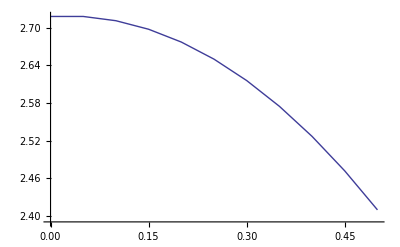

```mathematica
f[x_,y_]:=-(x y)/(√(1-x^2));
y0=ⅇ;
a=0;
b=0.5;
h=0.05;
(*n=(b-a)/h+1;*)
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Y[[1]]=y0;
For[i=2,i≤n,i++,
Y[[i]]=Y[[i-1]]+h*f[X[[i-1]],Y[[i-1]]];
];
Print[Y];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y[[i]]};
]
ListLinePlot[dots]
```

11

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{-1,-1.,-1.01111,-1.03471,-1.07235,-1.12582,-1.19714,-1.28865,-1.403,-1.54324,-1.71289}

{1,0.9,0.809091,0.726522,0.651599,0.583681,0.522173,0.466529,0.416244,0.370851,0.329922}

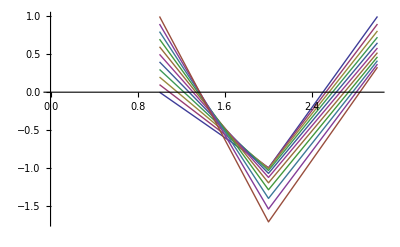

```mathematica
f1[x_,y_,z_]:=1-1/z;(*y'*)
f2[x_,y_,z_]:=1/(y-x); (*z'*)
y0=-1;
z0=1;
a=0;
b=1;
h=0.1;
(*n=(b-a)/h+1;*)
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Z=Table[{},{n}];
Y[[1]]=y0;
Z[[1]]=z0;
For[i=2,i≤n,i++,
Y[[i]]=Y[[i-1]]+h*f1[X[[i-1]],Y[[i-1]],Z[[i-1]]];
Z[[i]]=Z[[i-1]]+h*f2[X[[i-1]],Y[[i-1]],Z[[i-1]]];
];
Print[Y];
Print[Z];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y[[i]],Z[[i]]};
]
ListLinePlot[dots]
```